# Rabi Flopping - Process

## Last Updated: 2025/03/23

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

```mathematica
(*todo: fit distribution to something*)
(*todo: check that initial state has requisite dimensions*)
```

# General

## Values

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

## Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

## Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

## Units

```mathematica
(*frequency*)
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2.π*{10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[BarChart,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Evaluations

```mathematica
(*scde2={
Off[General::munfl],
Off[FindRoot::lstol],
Off[FindFit::cvmit],
Off[FindFit::sszero],
Off[FindFit::nrjnum],
Off[NonlinearModelFit::cvmit],
Off[NonlinearModelFit::sszero],
Off[Power::infy],
Off[Infinity::indet],
Off[FittedModel::constr]
};*)
```

```mathematica
(*Evaluate[#]&/@scde2*)
```

```mathematica
(*scde={
General::munfl,
FindRoot::lstol,
FindFit::cvmit,
FindFit::sszero,
FindFit::nrjnum,
NonlinearModelFit::cvmit,
NonlinearModelFit::sszero,
Power::infy,
Infinity::indet,
FittedModel::constr
};*)
```

```mathematica
(*Off[#]&/@scde*)
```

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
];
```

## Functions

## Phonon Conversion

```mathematica
coherentX0="0\t9.99968345065521e-05\t0.000399949359050543\t0.000899743688795304\t0.00159919018917467\t0.00249802373567682\t0.00359590407662662\t0.00489241629804741\t0.00638707138943964\t0.00807930690905264\t0.00996848774698177\t0.0120539069841832\t0.0143347868452619\t0.0168102797426638\t0.0194794694096749\t0.0223413721194334\t0.0253949379869404\t0.0286390523508750\t0.0320725372318338\t0.0356941528634366\t0.0395025992925868\t0.0434965180450157\t0.0476744938521131\t0.0520350564349007\t0.0565766823409077\t0.0612977968295938\t0.0661967758018701\t0.0712719477691913\t0.0765215958576296\t0.0819439598422616\t0.0875372382071775\t0.0932995902263676\t0.0992291380607130\t0.105323968866310\t0.111582136909319\t0.118001665682565\t0.124580550019086\t0.131316758197884\t0.138208234037120\t0.145252898970045\t0.152448654098991\t0.159793382222768\t0.167284949832890\t0.174921209074062\t0.182699999664427\t0.190619150771128\t0.198676482836768\t0.206869809352429\t0.215196938572920\t0.223655675170015\t0.232243821819463\t0.240959180717564\t0.249799555023207\t0.258762750221224\t0.267846575402984\t0.277048844460143\t0.286367377187489\t0.295800000290804\t0.305344548295672\t0.314998864353126\t0.324760800938008\t0.334628220435874\t0.344598995614207\t0.354671009973656\t0.364842157974930\t0.375110345136883\t0.385473488001222\t0.395929513959161\t0.406476360935198\t0.417111976923057\t0.427834319368674\t0.438641354394938\t0.449531055862707\t0.460501404262433\t0.471550385430509\t0.482675989084237\t0.493876207169105\t0.505149032011798\t0.516492454272143\t0.527904460686948\t0.539383031598436\t0.550926138259732\t0.562531739909640\t0.574197780608683\t0.585922185828196\t0.597702858784029\t0.609537676506275\t0.621424485636251\t0.633361097941900\t0.645345285542670\t0.657374775834950\t0.669447246109191\t0.681560317849959\t0.693711550710419\t0.705898436153020\t0.718118390748662\t0.730368749127130\t0.742646756572379\t0.754949561257081\t0.767274206112027\t0.779617620327223\t0.791976610483122";
coherentX0=Internal`StringToMReal/@StringSplit[coherentX0,"\t"];
```

```mathematica
coherentY0="0\t0.000100000000000000\t0.000400000000000000\t0.000900000000000000\t0.00160000000000000\t0.00250000000000000\t0.00360000000000000\t0.00490000000000000\t0.00640000000000000\t0.00810000000000000\t0.0100000000000000\t0.0121000000000000\t0.0144000000000000\t0.0169000000000000\t0.0196000000000000\t0.0225000000000000\t0.0256000000000000\t0.0289000000000000\t0.0324000000000000\t0.0361000000000000\t0.0400000000000000\t0.0441000000000000\t0.0484000000000000\t0.0529000000000000\t0.0576000000000000\t0.0625000000000000\t0.0676000000000000\t0.0729000000000000\t0.0784000000000000\t0.0841000000000000\t0.0900000000000000\t0.0961000000000000\t0.102400000000000\t0.108900000000000\t0.115600000000000\t0.122500000000000\t0.129600000000000\t0.136900000000000\t0.144400000000000\t0.152100000000000\t0.160000000000000\t0.168100000000000\t0.176400000000000\t0.184900000000000\t0.193600000000000\t0.202500000000000\t0.211600000000000\t0.220900000000000\t0.230400000000000\t0.240100000000000\t0.250000000000000\t0.260100000000000\t0.270400000000000\t0.280900000000000\t0.291600000000000\t0.302500000000000\t0.313600000000000\t0.324900000000000\t0.336400000000000\t0.348100000000000\t0.360000000000000\t0.372100000000000\t0.384400000000000\t0.396900000000000\t0.409600000000000\t0.422500000000000\t0.435600000000000\t0.448900000000000\t0.462400000000000\t0.476100000000000\t0.490000000000000\t0.504100000000000\t0.518400000000000\t0.532900000000000\t0.547600000000000\t0.562500000000000\t0.577600000000000\t0.592900000000000\t0.608400000000000\t0.624100000000000\t0.640000000000000\t0.656100000000000\t0.672400000000000\t0.688900000000000\t0.705600000000000\t0.722500000000000\t0.739600000000000\t0.756900000000000\t0.774400000000000\t0.792100000000000\t0.810000000000000\t0.828100000000000\t0.846400000000000\t0.864900000000000\t0.883600000000000\t0.902500000000000\t0.921600000000000\t0.940900000000000\t0.960400000000000\t0.980100000000000\t1\t1.02010000000000";
coherentY0=Internal`StringToMReal/@StringSplit[coherentY0,"\t"];
```

```mathematica
CoherentC=Interpolation[Transpose[{coherentX0,coherentY0}]];
```

## Dataset Processing

#### Import

```mathematica
(*import dataset from dir and filename, return dataset and parameters*)
ImportDatasetARTIQ[filedir_String,ridName:(_String|_Integer)]:=Module[
{
filenamesAll,
(*select file with give RID from all subdirectories*)
filenameDJ,
(*dataset values*)
datasetRaw,
parameterList
},

(*ensure import directory exists*)
If[!DirectoryQ[filedir],
(*stop execution if import directory doesn't exist*)
MessageDialog["Failure :(\nError: Import directory not found ("<>filedir<>")."];
FrontEndTokenExecute["EvaluatorAbort"],

(*get all files in directory*)
filenamesAll=FileNames["*.h5",filedir,Infinity];
];

(*ensure desired file exists*)
filenameDJ=SelectFirst[
filenamesAll,
StringContainsQ[#,ToString[ridName]]&
];

(*stop execution if file doesn't exist*)
If[!FileExistsQ[filenameDJ],
MessageDialog["Failure :(\nError: Specified file not found ("<>filenameDJ<>")."];
FrontEndTokenExecute["EvaluatorAbort"]
];

(*extract file results as list and parameters as an association*)
datasetRaw=Import[filenameDJ,{"/datasets/results"}];
parameterList=Import[filenameDJ,{"Attributes","/arguments"}];

Return[{datasetRaw,parameterList}];
];
```

#### Processing

```mathematica
(*threshold counts into s-state vs d-state probability*)
ThresholdCounts[dataset_List,countsColumn_Integer]:=Module[
{
(*find state discrimination threshold*)
countThreshold=FindThreshold[dataset[[;;,countsColumn]],Method->"MinimumError"],
results=dataset
},
(*directly threshold counts into D-state probability*)
results[[;;,countsColumn]]=1.-UnitStep[results[[;;,countsColumn]]-countThreshold];
(*Print[countThreshold];*)
Return[results];
];
```

```mathematica
(*group the data as desired, then take the mean of whatever remains*)
CollateData[dataset_List,groupColumnList_List]:=GroupBy[dataset,
Table[
With[{i=i},#[[i]]&],
{i,groupColumnList}
],
N[Mean[#]]&
]//KeySort;
```

#### Analysis

```mathematica
(*sinc-squared function for spetroscopy fitting*)
SincModel[α_,β_,δ_,t_,x_]:=α*Sinc[(π*t)*((x-β)*khz)+0.0000000001]^2+δ;
```

```mathematica
(*fit sinc and return params with error and confidence intervals*)
FitSinc[dataset_List,timeSinc:(_Integer|_Real)]:=Module[
{
guessMax=dataset[[First@Ordering[dataset[[;;,2]],-1]]],
guessOffset=Mean[{Median[dataset[[;;,2]]],Mean[dataset[[;;,2]]]}],
guessParamList,

α,β,γ,δ,x,
sincConstraints,
sincModel,

fitResult
},

(*create sinc model*)
sincModel=α*Sinc[(π*timeSinc)*((x-β)*khz)+0.00000001]^2+δ;

(*guess sinc fit parameters*)
guessParamList={
(guessMax[[2]]-guessOffset),(*rabi frequency*)
guessMax[[1]],(*resonance frequency*)
guessOffset (*background offset*)
};

(*constrain search range for parameters*)
sincConstraints={
(*α>0,α<αRSBguess*3,*)
(*β>0.975*βRSBguess,β<1.025*βRSBguess*)
δ>0
};

(*fit sinc model - nonlinearmodelfit to extract extra fit information*)
fitResult=NonlinearModelFit[
dataset,
Join[{sincModel,sincConstraints}],
Transpose[{{α,β,δ},guessParamList}],
x,
MaxIterations->10^4
];

(*todo: return parameters and their error*)
Return[fitResult["ParameterConfidenceIntervalTableEntries"]];
];
```

## Batch Processing

```mathematica
(*(*batch process eggs data for calibration (i.e. w/ sideband sweep), returning relevant values*)
ProcessDatasetEGGS[filedir_,filekey_]:=Module[
{
(*actual data*)
(*datafile=ImportDatasetARTIQ[filedir,ToString[filekey]],*)
datafile,
heatingTimeSeconds,
results=<||>,

(*processing*)
datasetProcessed,
rsbData,bsbData,

(*analysis*)
sidebandRatio,phononData,
rsbFitParams,phononFitParams
},

(*import dataset*)
datafile=ImportDatasetARTIQ[filedir,ToString[filekey]];

(*extract heating time from parameter list*)
heatingTimeSeconds=datafile[[2]]["time_eggs_heating_ms"]*ms;

(*convert dataset into correct units*)
datasetProcessed=Transpose[
Transpose[datafile[[1]]]*
{ftwToFrequencyMHz,1.,1.*^-6,1.*^-3}
];
(*threshold ion fluorescence counts into D-state probability*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
(*collate data by rsb/bsb and sideband frequency*)
datasetProcessed=CollateData[datasetProcessed,{1,4}];

(*separate rsb/bsb data as 2-D datasetss*)
{rsbData,bsbData}=SortBy[
Values[#][[;;,{4,2}]],
First
]&/@Values[datasetProcessed];
(*fit rsb*)
rsbFitParams=FitSinc[rsbData,heatingTimeSeconds];

(*add intermediate results*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"ParameterList"->datafile[[2]],
"BSBData"->bsbData,
"RSBData"->rsbData,
"RSBFitParams"->rsbFitParams,
"SBPlot"->Show[
ListPlot[
{rsbData,bsbData}
],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@rsbFitParams[[;;,1]],
{δ,rsbData[[1,1]],rsbData[[-1,1]]}
]]
}];

(*subtract background and create rsb/bsb ratio array*)
sidebandRatio=Transpose[{
rsbData[[;;,1]],
Ramp[(rsbData[[;;,2]]-rsbFitParams[[3,1]])/(bsbData[[;;,2]]-rsbFitParams[[3,1]])]
}];
(*convert to phonon number assuming coherent state*)
phononData=sidebandRatio;
phononData[[;;,2]]=CoherentC[sidebandRatio[[;;,2]]];
(*fit sinc to phonon number*)
phononFitParams=FitSinc[sidebandRatio,heatingTimeSeconds];

(*add intermediate computations to output*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"SidebandRatioData"->sidebandRatio,
"PhononData"->phononData,
"PhononFitParams"->phononFitParams,
"PhononPlot"->Show[
ListPlot[phononData],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@phononFitParams[[;;,1]],
{δ,phononData[[1,1]],phononData[[-1,1]]}
]]
}];


(*clean up mess*)
Remove[datafile,datasetProcessed,rsbData,bsbData,sidebandRatio,phononData,rsbFitParams,phononFitParams];
(*Remove[datafile];*)
ClearSystemCache[];

(*return dataset*)
Return[results];
];*)
```

```mathematica
(*batch process eggs data for calibration (i.e. w/ sideband sweep), returning relevant values*)
ProcessDatasetEGGS2[dataset_List,parameterList_Association]:=Module[
{
(*actual data*)
heatingTimeSeconds,
results=<||>,

(*processing*)
datasetProcessed,
rsbData,bsbData,

(*analysis*)
sidebandRatio,phononData,
rsbFitParams,phononFitParams
},

(*extract heating time from parameter list*)
heatingTimeSeconds=parameterList["time_eggs_heating_ms"]*ms;

(*convert dataset into correct units*)
datasetProcessed=Transpose[
Transpose[dataset]*
{ftwToFrequencyMHz,1.,1.*^-6,1.*^-3}
];
(*threshold ion fluorescence counts into D-state probability*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
(*collate data by rsb/bsb and sideband frequency*)
datasetProcessed=CollateData[datasetProcessed,{1,4}];

(*separate rsb/bsb data as 2-D datasetss*)
{rsbData,bsbData}=SortBy[
Values[#][[;;,{4,2}]],
First
]&/@Values[datasetProcessed];
(*fit rsb*)
rsbFitParams=FitSinc[rsbData,heatingTimeSeconds];

(*add intermediate results*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"ParameterList"->parameterList,
"BSBData"->bsbData,
"RSBData"->rsbData,
"RSBFitParams"->rsbFitParams,
"SBPlot"->Show[
ListPlot[
{rsbData,bsbData}
],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@rsbFitParams[[;;,1]],
{δ,rsbData[[1,1]],rsbData[[-1,1]]}
]]
}];

(*subtract background and create rsb/bsb ratio array*)
sidebandRatio=Transpose[{
rsbData[[;;,1]],
Ramp[(rsbData[[;;,2]]-rsbFitParams[[3,1]])/(bsbData[[;;,2]]-rsbFitParams[[3,1]])]
}];
(*convert to phonon number assuming coherent state*)
phononData=sidebandRatio;
phononData[[;;,2]]=CoherentC[sidebandRatio[[;;,2]]];
(*fit sinc to phonon number*)
phononFitParams=FitSinc[sidebandRatio,heatingTimeSeconds];

(*add intermediate computations to output*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"SidebandRatioData"->sidebandRatio,
"PhononData"->phononData,
"PhononFitParams"->phononFitParams,
"PhononPlot"->Show[
ListPlot[phononData],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@phononFitParams[[;;,1]],
{δ,phononData[[1,1]],phononData[[-1,1]]}
]]
}];


(*clean up mess*)
Remove[datasetProcessed,rsbData,bsbData,sidebandRatio,phononData,rsbFitParams,phononFitParams];
ClearSystemCache[];

(*return dataset*)
Return[results];
];
```

## Motional States

### State Vectors

```mathematica
(*create a thermal state phonon vector*)
ThermalState[nAvg_:(_Integer|_Real),numPhonons_Integer]:=Module[
{phononArr=Array[
(1./(nAvg+1.))*(nAvg/(nAvg+1.))^#&,
IntegerPart[numPhonons+1],
0
]},

(*return normalized probabilities*)
Return[#/Total[#]&[phononArr]]
];
```

```mathematica
(*create a coherent state phonon vector*)
CoherentState[α_:(_Integer|_Real),numPhonons_Integer]:=Module[
{phononArr=Exp[-Abs[α]^2.]*Array[
(Abs[α]^(2.*#)/(#!))&,
IntegerPart[numPhonons+1],
0
]},

(*return normalized probabilities*)
Return[#/Total[#]&[phononArr]]
];
```

```mathematica
(*create a squeezed state phonon vector*)
SqueezedState[r_:(_Integer|_Real),numPhonons_Integer]:=Module[
{phononArr=Array[
Abs[Tanh[r]^#/(2.^#*Cosh[r])(#!)/((#/2)!)^2.]&,
IntegerPart[numPhonons+1],
0
]},

(*ensure odd-numbered fock states have 0 population*)
phononArr[[2;;;;2]]=0.;
(*return normalized probabilities*)
Return[#/Total[#]&[phononArr]]
];
```

```mathematica
(*create a squeezed coherent state phonon vector*)
SqueezedCoherentState[
r_:(_Integer|_Real|_Complex),
ϕs_:(_Integer|_Real|_Complex),
α_:(_Integer|_Real|_Complex),
numPhonons_Integer
]:=Module[
{
coefficient=Exp[-Abs[α]^2.*(1.-Tanh[r]*Cos[2.*Arg[α]-ϕs])],
hermiteArr=
Array[
Abs[HermiteH[#,(Abs[α]*Exp[ⅈ*(Arg[α]-ϕs/2.)])/Sqrt[Sinh[2.*r]]]]^2.&,
IntegerPart[numPhonons+1],
0
],
phononArr=Array[
Abs[(Tanh[r]/2.)^#/((#!)*Cosh[r])]&,
IntegerPart[numPhonons+1],
0
]
},
(*Print[coefficient];
Print[hermiteArr[[1]]];
Print[phononArr[[1]]];
Print[Total[#]&[coefficient*(hermiteArr*phononArr)]];*)
(*return normalized probabilities*)
Return[#/Total[#]&[coefficient*(hermiteArr*phononArr)]];
];
```

### Convert to Function

```mathematica
(*specify optional arguments and their default value for DistributionToModel function*)
Options[DistributionToModel]={
"Δn"->1
};
```

```mathematica
(*create a symbolic model from a given phonon state distribution*)
DistributionToModel[
dist_List,
A_:(_Integer|_Real),Ω_:(_Integer|_Real),β_:(_Integer|_Real),η_:(_Integer|_Real),
OptionsPattern[]
]:=Block[{t},
Module[
{
Δn=OptionValue["Δn"],
numPhonons=Length[dist]-1,
βnArr,
ΩnArr
},

(*create model objects*)
βnArr=Array[Exp[-1./β*√(#+1.)*t]&,IntegerPart[numPhonons+1],0];
ΩnArr=(η*Exp[-η^2./2.])^Abs[Δn]*Array[LaguerreL[#,Abs[Δn],η^2.]&,IntegerPart[numPhonons+1],0];

(*set raising/lowering coefficients correctly*)
If[Δn>0,
(*BSB case*)
ΩnArr*=(1.+Range[0,IntegerPart[numPhonons]])^(-0.5*Abs[Δn]),
If[
Δn<0,
(*RSB case*)
ΩnArr*=Join[{0},(Range[1,IntegerPart[numPhonons]])^(-0.5*Abs[Δn])],
Null
]
];

(*return expression as function of t*)
Return[dist.(A/2.*(1.-βnArr*Cos[ΩnArr*Ω*t]))];
]];
```

# Fit Functions - Distribution

## Normal Fit (Nonlinear)

```mathematica
(*specify optional arguments and their default value for FitFockSpectrum function*)
Options[FitFockSpectrum]={
"InitialState"->{},
"numPhonons"->20,
"Constraints"->{}
};
```

```mathematica
(*fit arbitrary fock state distribution to rabi flopping data and return object*)
FitFockSpectrum[
dataset_List,
A0:(_Integer|_Real),Ω0:(_Integer|_Real),β0:(_Integer|_Real),η0_:(_Integer|_Real),
Δn_Integer,
OptionsPattern[]
]:=Block[{
(*local variables*)
A,Ω,β,η,t,Pn,

(*keyword arguments*)
initialState=OptionValue["InitialState"],
numPhonons=OptionValue["numPhonons"],
constraints=OptionValue["Constraints"]
},
Module[
{
(*data structures for fitting*)
PnArr=Array[Pn,IntegerPart[numPhonons+1],0],
βnArr=Array[Exp[-t/β*√(#+1)]&,IntegerPart[numPhonons+1],0],
ΩnArr=(η*Exp[-η^2./2.])^Abs[Δn]*Array[LaguerreL[#,Abs[Δn],η^2.]&,IntegerPart[numPhonons+1],0],

(*parameters & initial values*)
guessParamList={A0,Ω0,β0,η0},

(*fitting*)
fitConstraints,fitModel,fitResult
},

(*set raising/lowering coefficients correctly*)
If[Δn>0,
(*BSB case*)
ΩnArr*=(1.+Range[0,IntegerPart[numPhonons]])^(-0.5*Abs[Δn]),
If[
Δn<0,
(*RSB case*)
ΩnArr*=Join[{0},(Range[1,IntegerPart[numPhonons]])^(-0.5*Abs[Δn])],
Null
]
];

(*create fit model for rabi flopping*)
fitModel=PnArr.(A/2.*(1.-βnArr*Cos[ΩnArr*Ω0*t]));
(*(*tmp remove*)
fitModel=fitModel/.{A->ADJ,β->βDJ,Ω->ΩDJ,η->ηDJ};
(*tmp remove*)*)

(*set probability conservation constraints*)
fitConstraints={
(*0.<#<1.&/@PnArr,*)
(*Total[PnArr]==1.*)
}//Flatten;
fitConstraints=Join[fitConstraints,constraints];

(*fit!*)
fitResult=NonlinearModelFit[
dataset,
Join[{fitModel,fitConstraints}],
Transpose[{
Join[{A,Ω,β,η},PnArr],
Join[guessParamList,initialState]
}],
t,
MaxIterations->10^5
];
(*tmp remove - fit with fixed rabi flopping parameters*)
(*fitResult=NonlinearModelFit[
dataset,
Join[{fitModel,fitConstraints}],
Transpose[{
PnArr,
initialState
}],
t,
MaxIterations->10^8
];*)

(*return fit object*)
Return[fitResult];
]];
```

## Linear Least Squares

```mathematica
(*specify optional arguments and their default value for FitFockSpectrum function*)
Options[FitFockSpectrumLSQ]={
"numPhonons"->20
};
```

```mathematica
(*fit arbitrary fock state distribution to rabi flopping data and return object*)
FitFockSpectrumLSQ[
dataset_List,
A0:(_Integer|_Real),Ω0:(_Integer|_Real),β0:(_Integer|_Real),η0_:(_Integer|_Real),
Δn_Integer,
OptionsPattern[]
]:=Block[{
(*local variables*)
A,Ω,t,Pn,

(*keyword arguments*)
numPhonons=OptionValue["numPhonons"]
},
Module[
{
(*separate out dataset dimensions*)
datasetX=dataset[[;;,1]],
datasetY=dataset[[;;,2]],

(*data structures for fitting - phenomenological decay*)
βnArr=Array[Exp[-1/β0*√(#+1)]&,IntegerPart[numPhonons+1],0],
(*data structures for fitting - rabi frequency (necessary since this supports arbitrary order sideband)*)
ΩnArr=(η0*Exp[-η0^2./2.])^Abs[Δn]*Array[LaguerreL[#,Abs[Δn],η0^2.]&,IntegerPart[numPhonons+1],0],

(*least squares fitting*)
fitBasisMat,fitResult
},

(*set raising/lowering coefficients correctly for RSB/BSB flopping*)
If[Δn>0,
(*BSB case*)
ΩnArr*=(1.+Range[0,IntegerPart[numPhonons]])^(-0.5*Abs[Δn]),
(*RSB case*)
If[Δn<0,
ΩnArr*=Join[{0},(Range[1,IntegerPart[numPhonons]])^(-0.5*Abs[Δn])],
(*ignore the carrier case*)
Null
]
];

(*create linear least squares design matrix - rows:phonon num, columns:time steps*)
fitBasisMat=A0/2.*(1.-(βnArr^#*Cos[ΩnArr*Ω0*#]&/@datasetX));

(*do least squares fit*)
(*fitResult=LeastSquares[fitBasisMat,datasetY];*)
fitResult=LinearModelFit[{fitBasisMat,datasetY}];
(*normalize the result*)
(*fitResult=fitResult/Total[Abs[fitResult]];*)

(*return normalized state probabilities*)
Return[fitResult];
]];
```

# User Input

## Parameters

```mathematica
(*top level directory for imports*)
(*directoryString="/Users/claytonho/Documents/Research/Data & Analysis/Rabi Flopping/Datasets/2024_09_fock_state_decomposition_test";*)
(*directoryString="Z:\\motion\\Data\\2025-03\\2025-03-21";*)
directoryString="/Volumes/groups/motion/Data/2025-03/2025-03-22";
```

```mathematica
(*select runs*)
rid=102801;
```

## Validate User Input

```mathematica
(*check input directory exists*)
If[!DirectoryQ[directoryString],
MessageDialog["Failure :(\nError: Import directory not found ("<>directoryString<>")."];
FrontEndTokenExecute["EvaluatorAbort"];
];
```

# Import & Process

## Import

```mathematica
(*import dataset*)
datafile=ImportDatasetARTIQ[directoryString,#]&[rid];
{dataset,parameters}=datafile;
```

```mathematica
(*todo: preplot & threshold etc for vibes*)
```

```mathematica
(*get important parameters*)
paramRepetitions=parameters["repetitions"];
```

```mathematica
(*get the sweep index*)
uniqueElements=Length/@(DeleteDuplicates/@Transpose[dataset])
sweepIndex=Ordering[uniqueElements]//Reverse;
(*ensure that unique index is not for counts*)
sweepIndex=If[First@sweepIndex==2,
sweepIndex[[2]],
sweepIndex[[1]]
];
```

{200,120,1}

```mathematica
(*(*tmp remove*)
(*batch import*)
dirTMP="/Users/claytonho/Documents/Research/Data & Analysis/Rabi Flopping/Datasets/2023_10_02_squeezing_strength";
ridList=FileNames["*.h5",dirTMP];
ridList=ToExpression[StringSplit[StringSplit[#,"/"][[-1]],"-"][[1]]]&/@ridList;
datafileArr=ImportDatasetARTIQ[dirTMP,#]&/@ridList;

(*combine!*)
datafileArr2=datafileArr[[;;,1]];
dataset=Join@@datafileArr2;
(*tmp remove*)*)
```

```mathematica
(*extract & convert units: readout freq, secular frequency, time, counts*)
(*for normal rabi flopping data*)
(*dataset[[;;,1]]*=ns;*)
(*(*for eggs rabi flopping exp data*)
dataset=dataset[[;;,{1,4,5,2}]];
dataset=Transpose[Transpose[dataset]*{ftwToFrequencyMHz,1./khz,ns,1}];*)
(*(*for squeezing exp data*)
dataset=dataset[[;;,{1,5,sweepIndex,2}]];
dataset=Transpose[Transpose[dataset]*{ftwToFrequencyMHz,1./1000,ns,1}];*)
```

```mathematica
(*select BSB and remove readout frequency from the dataset*)
(*freqCenter=Mean[dataset[[;;,1]]];
dataset=Select[dataset,#[[1]]>=freqCenter&][[;;,{2,3,4}]];*)
(*dataset=dataset[[;;,{2,3,4}]];*)
```

## Batch Import

```mathematica
(*BatchProcess[ds_List]:=Module[
{dataset=ds},
dataset=ThresholdCounts[dataset,2];
dataset=CollateData[dataset,{1}];
dataset=SortBy[
Values[dataset][[;;,{1,2}]],
First
];
Return[dataset];
];*)
```

```mathematica
(*dirTMP="/Users/claytonho/Documents/Research/Data & Analysis/Rabi Flopping/Datasets/2023_10_02_squeezing_strength";
ridList=FileNames["*.h5",dirTMP];
ridList=ToExpression[StringSplit[StringSplit[#,"/"][[-1]],"-"][[1]]]&/@ridList;*)
```

```mathematica
(*datafileArr=ImportDatasetARTIQ[dirTMP,#]&/@ridList;
th0=BatchProcess/@datafileArr[[;;,1]];
(*ListPlot/@th0*)*)
```

## Process

```mathematica
(*group & process data*)
datasetProcessed=dataset[[;;,{sweepIndex,2}]];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ns,1.}];
```

```mathematica
(*threshold counts & collate data by secular frequency then readout time*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
datasetProcessed=CollateData[datasetProcessed,{1}];
```

```mathematica
(*format dataset into bunch of 2-D lists*)
(*datasetProcessed=SortBy[
Values[#][[;;,{1}]],
First
]&/@datasetProcessed;*)
datasetProcessed=SortBy[
Values[datasetProcessed](*[[;;,{6,2}]]*),
First
];
```

```mathematica
(*tmp remove*)
(*datasetProcessed[[;;,1]]*=ns;*)
datasetProcessed={datasetProcessed};
```

# Fit Arbitrary Distribution

## Fit!

```mathematica
(*specify variables & parameters*)
ADJ=0.99;
ΩDJ=455.71*wkhz/2.;
βDJ=10.*ms;
ηDJ=0.05;
```

```mathematica
(*yzde[η_]:=1/η*(η*Exp[-η^2./2.])^Abs[1]*Array[LaguerreL[#,Abs[1],η^2.]/(√(#+1.))^2&,IntegerPart[30+1],0];*)
```

```mathematica
(*constraints*)
constraintsDJ={
(*A==ADJ;
Ω==ΩDJ,
η==ηDJ,
β==βDJ*)
};
```

```mathematica
(*fit states & distribution*)
numPhononsDJ=10;
(*initialState=UnitVector[numPhononsDJ+1,1];*)
initialState=CoherentState[1.2,numPhononsDJ];
```

## Actual Fit

```mathematica
(*fit - nonlinear model fit*)
AbsoluteTiming[
fitDistResNonlinear=ParallelMap[
FitFockSpectrum[
#,
ADJ,ΩDJ,βDJ,ηDJ,1,
"numPhonons"->numPhononsDJ,
"InitialState"->initialState,
"Constraints"->constraintsDJ
]&,
datasetProcessed
];
]
```

{0.067177,Null}

```mathematica
(*fit - linear least squares (LLSQ) fit*)
AbsoluteTiming[
fitDistResLLSQ=ParallelMap[
FitFockSpectrumLSQ[
#,
ADJ,ΩDJ,βDJ,ηDJ,1,
"numPhonons"->numPhononsDJ
]&,
datasetProcessed
];
]
```

{0.021475,Null}

```mathematica
(*create dataset iterator for convenience*)
(*datasetIter=Range[Length[fitDistResNonlinear]];*)
datasetIter={1};
```

## Process Fit Results

```mathematica
(*get fit params - nonlinear*)
fitDistNonlinearResParams=Style[
fitDistResNonlinear[[#]]["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
]&/@datasetIter;

(*get fit params - linear least squares (LLSQ)*)
fitDistLLSQResParams=Style[
fitDistResLLSQ[[#]]["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
]&/@datasetIter;
(*quick fix - make the row labels for LLSQ fit more descriptive*)
fitDistLLSQResParams[[;;,1,1,2;;,1]]=Array[Pn,numPhononsDJ+1,0];
```

```mathematica
(*get raw fitted results with error bars*)
(*note: for nonlinear fit, we slice [[5;;,;;2]] b/c first 4 fit vals are rabi flopping params*)
fitDistNonlinearValues=fitDistResNonlinear[[#]]["ParameterConfidenceIntervalTableEntries"][[5;;,1]]&/@datasetIter;
fitDistLLSQValues=fitDistResLLSQ[[#]]["ParameterConfidenceIntervalTableEntries"][[;;,1]]&/@datasetIter;

(*get raw fitted results with error bars*)
(*note: for nonlinear fit, we slice [[5;;,;;2]] b/c first 4 fit vals are rabi flopping params*)
fitDistNonlinearValuesErr=Around@@@fitDistResNonlinear[[#]]["ParameterConfidenceIntervalTableEntries"][[5;;,;;2]]&/@datasetIter;
fitDistLLSQValuesErr=Around@@@fitDistResLLSQ[[#]]["ParameterConfidenceIntervalTableEntries"][[;;,;;2]]&/@datasetIter;
```

## Plot

## Plot Raw Data

```mathematica
(*plot raw time-series data*)
rawDataPlots=ListPlot[
{
datasetProcessed[[#]],
datasetProcessed[[#]]
},
PlotRange->{Automatic,{0.,1.}},
Joined->{False,True},
PlotStyle->{
{Automatic,PointSize[0.01]},
{Opacity[0.4],Dashed,Blue,Thickness[0.003]}
},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Time (s)",{Black,Directive[15]}],
Style["BSB Rabi Flopping\nRID: "<>ToString[rid],{Black,Directive[15]}](*todo - do RID*)
}
},
ImageSize->Scaled[0.45]
]&/@datasetIter;
```

## Plot Fitted Models (Time-Domain)

```mathematica
(*create time-domain models for the LLSQ fit*)
fitDistLLSQModel=DistributionToModel[fitDistLLSQValues[[#]],ADJ,ΩDJ,βDJ,ηDJ]&/@datasetIter;
```

```mathematica
(*plot models of distribution fits*)
fitModelPlots=Plot[
{
fitDistResNonlinear[[#]]["BestFit"],
fitDistLLSQModel[[#]]
},
{t,datasetProcessed[[#]][[1,1]],datasetProcessed[[#]][[-1,1]]},
PlotRange->{Automatic,{0.,1.}},
PlotStyle->{{Red},{Brown},{Black}},
PlotLabels->Placed[{
Style["Distribution Fit (Nonlinear)",{FontColor->Red,FontSize->14}],
Style["Distribution Fit (LLSQ)",{FontColor->Brown,FontSize->14}]
},Above],
PlotLegends->{
"Distribution Fit (Nonlinear)",
"Distribution Fit (LLSQ)"
},
PerformanceGoal->"Speed",
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Time (s)",{Black,Directive[15]}],
Style["BSB Rabi Flopping\nRID: "<>ToString[rid],{Black,Directive[15]}](*todo - do RID*)
}
},
ImageSize->Scaled[0.45]
]&/@datasetIter;
```

## Plot Models (Fock-State Histogram)

```mathematica
(*show fock state distribution*)
fitDistFockHistogram=
ListPlot[
{
Transpose[{Range[0,numPhononsDJ],fitDistNonlinearValuesErr[[#]]}],
Transpose[{Range[0,numPhononsDJ],fitDistNonlinearValues[[#]]}],
Transpose[{Range[0,numPhononsDJ],fitDistLLSQValuesErr[[#]]}],
Transpose[{Range[0,numPhononsDJ],fitDistLLSQValues[[#]]}]
},
(*PlotRange->{{-0.1,numPhononsDJ},{-1.,1.}},*)
PlotRange->{{Automatic,Automatic},{Automatic,Automatic}},
Joined->{False,True,False,True},
PlotStyle->{
{Automatic,Red,PointSize[0.01]},
{Opacity[0.4],Dashed,Red,Thickness[0.003]},
{Automatic,Brown,PointSize[0.01]},
{Opacity[0.4],Brown,Dashed,v,Thickness[0.003]}
},
PlotLabels->Placed[{
Style["Distribution Fit - Nonlinear",{FontColor->Red,FontSize->14}],
None,
Style["Distribution Fit - LLSQ",{FontColor->Brown,FontSize->14}],
None
},Above],
PlotLegends->{
"Distribution Fit - Nonlinear",
None,
"Distribution Fit - LLSQ",
None
(*"Initial Guess"*)
},
FrameLabel->{ 
{Style["Probability",{Black,Directive[15]}],None},
{
Style["Fock State",{Black,Directive[15]}],
Style["Fock State Distribution - Fitted\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotRange->{Automatic,Automatic}
]&/@datasetIter;
```

```mathematica
(*create bar charts*)
fitDistNonlinearFockBarChart=BarChart[
fitDistNonlinearValuesErr[[#]],
ChartLabels->Range[0,numPhononsDJ-1],
(*PlotRange->{{Full,Full},{Full,Full}},*)
PlotRange->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{ 
{Style["Probability",{Black,Directive[15]}],None},
{
Style["Fock State",{Black,Directive[15]}],
Style["Fock State Distribution - Nonlinear LSQ\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
ImageSize->Scaled[0.45]
]&/@datasetIter;

fitDistLLSQFockBarChart=BarChart[
fitDistLLSQValuesErr[[#]],
ChartLabels->Range[0,numPhononsDJ-1],
(*PlotRange->{{Full,Full},{Full,Full}},*)
PlotRange->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{ 
{Style["Probability",{Black,Directive[15]}],None},
{
Style["Fock State",{Black,Directive[15]}],
Style["Fock State Distribution - SVD\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
ImageSize->Scaled[0.45]
]&/@datasetIter;
```

## Create Summary Figures

```mathematica
(*combine time-series plots*)
fitDistPlotsSummary={
Show[
rawDataPlots[[#]],
fitModelPlots[[#]]
]
}&/@datasetIter;
```

## Show

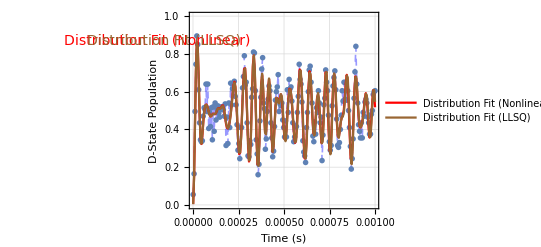

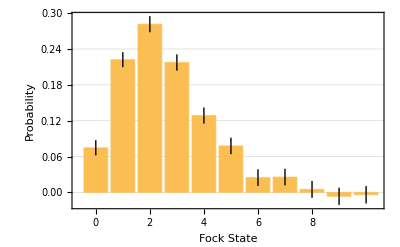
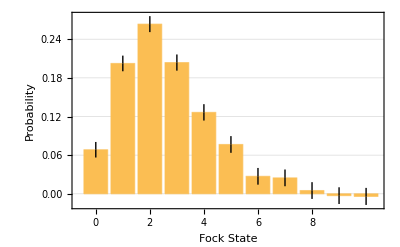

{{ | Estimate | Standard Error | Confidence Interval
A | 0.937685 | 0.00510637 | {0.927611,0.947759}
Ω | 1.43166×10^6 | 1.31088×10^-16 | {1.43166×10^6,1.43166×10^6}
β | 0.00841844 | 0.00286594 | {0.00276431,0.0140726}
η | 0.0500747 | 0.0000226758 | {0.0500299,0.0501194}
Pn[0] | 0.0746086 | 0.0127281 | {0.0494978,0.0997195}
Pn[1] | 0.22212 | 0.0125557 | {0.197349,0.246891}
Pn[2] | 0.281526 | 0.0134833 | {0.254925,0.308127}
Pn[3] | 0.217429 | 0.0135682 | {0.190661,0.244198}
Pn[4] | 0.128672 | 0.0134335 | {0.10217,0.155175}
Pn[5] | 0.0777489 | 0.0137751 | {0.0505724,0.104925}
Pn[6] | 0.0247776 | 0.0138795 | {-0.00260492,0.05216}
Pn[7] | 0.0256296 | 0.0139453 | {-0.0018827,0.0531419}
Pn[8] | 0.00504684 | 0.0141991 | {-0.0229661,0.0330598}
Pn[9] | -0.00654915 | 0.0144376 | {-0.0350326,0.0219343}
Pn[10] | -0.00401145 | 0.014568 | {-0.0327522,0.0247294}, | Estimate | Standard Error | Confidence Interval
Pn[0] | 0.0684042 | 0.0120745 | {0.0445861,0.0922223}
Pn[1] | 0.202376 | 0.0121375 | {0.178434,0.226319}
Pn[2] | 0.263431 | 0.0124027 | {0.238965,0.287896}
Pn[3] | 0.203744 | 0.0125488 | {0.178991,0.228498}
Pn[4] | 0.126429 | 0.012704 | {0.101369,0.151488}
Pn[5] | 0.0765854 | 0.0129618 | {0.051017,0.102154}
Pn[6] | 0.0271534 | 0.0129672 | {0.00157434,0.0527325}
Pn[7] | 0.0247279 | 0.0129917 | {-0.000899506,0.0503553}
Pn[8] | 0.00505099 | 0.013005 | {-0.0206026,0.0307046}
Pn[9] | -0.00285595 | 0.012969 | {-0.0284385,0.0227266}
Pn[10] | -0.00407269 | 0.0132305 | {-0.0301712,0.0220258}}}

```mathematica
(*Transpose[{fitDistPlotsSummary,fitDistFockHistogram}]*)
fitDistPlotsSummary
Transpose[{fitDistNonlinearFockBarChart,fitDistLLSQFockBarChart}]
Transpose[{fitDistNonlinearResParams,fitDistLLSQResParams}]
```

## Fit Fock State Distributions

## Fit!

```mathematica
(*specify variables & parameters*)
stateType="c";
stateParam=0.2;
```

### Actual Fit

```mathematica
yzx=Range[0,numPhononsDJ];
```

```mathematica
yzDefault=Transpose[{
yzx+0,
#["Value"]&/@fitDistLLSQValuesErr[[1]]
}];
yzWeights=1./(#["Uncertainty"])^2.&/@fitDistLLSQValuesErr[[1]];
```

```mathematica
yz0=NonlinearModelFit[
yzDefault,
(*Join[{fitModel,fitConstraints}],*)
{Exp[-Abs[α]^2.]*(Abs[α]^(2.*nDJ)/(nDJ!))},
{
{α,stateParam}
},
nDJ,
Weights->yzWeights
];
```

## Plot

```mathematica
(*adjust values for plotting*)
yz1=Transpose[{
yzx+1,
yz0[#]&/@yzx
}];
```

```mathematica
(*plot fitted state distribution*)
yzPlot=ListPlot[
{
yz1,
yz1
},
PlotRange->{
{Full,Full},
{Full,Full}
},
Joined->{False,True},
PlotStyle->{
{Automatic,PointSize[0.015]},
{Opacity[0.4],Dashed,Blue,Thickness[0.006]}
},
FrameLabel->{ 
{Style["Probability",{Black,Directive[15]}],None},
{
Style["Fock State",{Black,Directive[15]}],
Style["Fitted α: "<>ToString[α/.yz0["BestFitParameters"]]<>"\nRID: "<>ToString[rid],{Black,Directive[15]}](*todo - do RID*)
}
},
ImageSize->Scaled[0.45]
]&/@datasetIter;
```

## Show

```mathematica
(*calculate mean phonon number ⟨n⟩*)
nBarRes=Total[Range[0,numPhononsDJ]*(fitDistLLSQValuesErr[[1]])]["Value"];
```

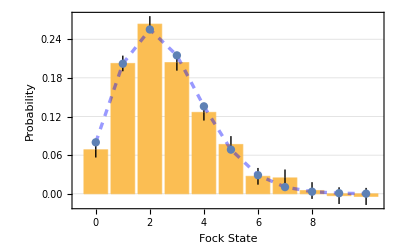

```mathematica
(*show fitted fock state decomp*)
Show[
fitDistLLSQFockBarChart,
yzPlot,
FrameLabel->{ 
{Style["Probability",{Black,Directive[16]}],None},
{
Style["Fock State",{Black,Directive[16]}],
Style["Fock State Distribution (SVD) - RID: "<>ToString[rid]<>"\n ⟨n⟩: "<>ToString[nBarRes]<>"\tFitted α: "<>ToString[α/.yz0["BestFitParameters"]],{Black,Directive[16]}](*todo - do RID*)
}
},
ImageSize->Scaled[0.5]
]
```

### Process Fit Results

```mathematica
(*get fit params - nonlinear*)
fitDistNonlinearResParams=Style[
fitDistResNonlinear[[#]]["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
]&/@datasetIter;

(*get fit params - linear least squares (LLSQ)*)
fitDistLLSQResParams=Style[
fitDistResLLSQ[[#]]["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
]&/@datasetIter;
```

```mathematica
(*get raw fitted results with error bars*)
(*note: for nonlinear fit, we slice [[5;;,;;2]] b/c first 4 fit vals are rabi flopping params*)
fitDistNonlinearValues=fitDistResNonlinear[[#]]["ParameterConfidenceIntervalTableEntries"][[5;;,1]]&/@datasetIter;
fitDistLLSQValues=fitDistResLLSQ[[#]]["ParameterConfidenceIntervalTableEntries"][[;;,1]]&/@datasetIter;

(*get raw fitted results with error bars*)
(*note: for nonlinear fit, we slice [[5;;,;;2]] b/c first 4 fit vals are rabi flopping params*)
fitDistNonlinearValuesErr=Around@@@fitDistResNonlinear[[#]]["ParameterConfidenceIntervalTableEntries"][[5;;,;;2]]&/@datasetIter;
fitDistLLSQValuesErr=Around@@@fitDistResLLSQ[[#]]["ParameterConfidenceIntervalTableEntries"][[;;,;;2]]&/@datasetIter;
```

## Plot

### Plot Models (Fock-State Histogram)

```mathematica
(*show fock state distribution*)
fitDistFockHistogram=
ListPlot[
{
Transpose[{Range[0,numPhononsDJ],fitDistNonlinearValuesErr[[#]]}],
Transpose[{Range[0,numPhononsDJ],fitDistNonlinearValues[[#]]}],
Transpose[{Range[0,numPhononsDJ],fitDistLLSQValuesErr[[#]]}],
Transpose[{Range[0,numPhononsDJ],fitDistLLSQValues[[#]]}]
},
(*PlotRange->{{-0.1,numPhononsDJ},{-1.,1.}},*)
Joined->{False,True,False,True},
PlotStyle->{
{Automatic,Red,PointSize[0.01]},
{Opacity[0.4],Dashed,Red,Thickness[0.003]},
{Automatic,Brown,PointSize[0.01]},
{Opacity[0.4],Brown,Dashed,v,Thickness[0.003]}
},
PlotLabels->Placed[{
Style["Distribution Fit - Nonlinear",{FontColor->Red,FontSize->14}],
None,
Style["Distribution Fit - LLSQ",{FontColor->Brown,FontSize->14}],
None
(*"Initial Guess",*)
},Above],
PlotLegends->{
"Distribution Fit - Nonlinear",
None,
"Distribution Fit - LLSQ",
None
(*"Initial Guess"*)
},
FrameLabel->{ 
{Style["Probability",{Black,Directive[15]}],None},
{
Style["Fock State",{Black,Directive[15]}],
Style["Fock State Distribution - Fitted\nRID: "<>ToString[rid],{Black,Directive[15]}](*todo - do RID*)
}
},
PlotRange->{Automatic,Automatic}
]&/@datasetIter;
```

```mathematica
(*create bar charts*)
fitDistNonlinearFockBarChart=BarChart[
fitDistNonlinearValuesErr[[#]],
ChartLabels->Range[0,numPhononsDJ-1],
PlotRange->{Full,Full},
FrameLabel->{ 
{Style["Probability",{Black,Directive[15]}],None},
{
Style["Fock State",{Black,Directive[15]}],
Style["Fock State Distribution - Nonlinear LSQ\nRID: "<>ToString[rid],{Black,Directive[15]}](*todo - do RID*)
}
},
PlotRange->{Automatic,Automatic},
ImageSize->Scaled[0.45]
]&/@datasetIter;

fitDistLLSQFockBarChart=BarChart[
fitDistLLSQValuesErr[[#]],
ChartLabels->Range[0,numPhononsDJ-1],
PlotRange->{Full,Full},
FrameLabel->{ 
{Style["Probability",{Black,Directive[15]}],None},
{
Style["Fock State",{Black,Directive[15]}],
Style["Fock State Distribution - SVD\nRID: "<>ToString[rid],{Black,Directive[15]}](*todo - do RID*)
}
},
PlotRange->{Automatic,Automatic},
ImageSize->Scaled[0.45]
]&/@datasetIter;
```

### Create Summary Figures

```mathematica
(*combine time-series plots*)
fitDistPlotsSummary={
Show[
rawDataPlots[[#]],
fitModelPlots[[#]]
]
}&/@datasetIter;
```

## Show

```mathematica
Transpose[{fitDistNonlinearFockBarChart,fitDistLLSQFockBarChart}]
Transpose[{fitDistNonlinearResParams,fitDistLLSQResParams}]
```

{{-Graphics-,-Graphics-}}

{{ | Estimate | Standard Error | Confidence Interval
A | 0.937685 | 0.00510637 | {0.927611,0.947759}
Ω | 1.43166×10^6 | 1.31088×10^-16 | {1.43166×10^6,1.43166×10^6}
β | 0.00841844 | 0.00286594 | {0.00276431,0.0140726}
η | 0.0500747 | 0.0000226758 | {0.0500299,0.0501194}
Pn[0] | 0.0746086 | 0.0127281 | {0.0494978,0.0997195}
Pn[1] | 0.22212 | 0.0125557 | {0.197349,0.246891}
Pn[2] | 0.281526 | 0.0134833 | {0.254925,0.308127}
Pn[3] | 0.217429 | 0.0135682 | {0.190661,0.244198}
Pn[4] | 0.128672 | 0.0134335 | {0.10217,0.155175}
Pn[5] | 0.0777489 | 0.0137751 | {0.0505724,0.104925}
Pn[6] | 0.0247776 | 0.0138795 | {-0.00260492,0.05216}
Pn[7] | 0.0256296 | 0.0139453 | {-0.0018827,0.0531419}
Pn[8] | 0.00504684 | 0.0141991 | {-0.0229661,0.0330598}
Pn[9] | -0.00654915 | 0.0144376 | {-0.0350326,0.0219343}
Pn[10] | -0.00401145 | 0.014568 | {-0.0327522,0.0247294}, | Estimate | Standard Error | Confidence Interval
#1 | 0.0684042 | 0.0120745 | {0.0445861,0.0922223}
#2 | 0.202376 | 0.0121375 | {0.178434,0.226319}
#3 | 0.263431 | 0.0124027 | {0.238965,0.287896}
#4 | 0.203744 | 0.0125488 | {0.178991,0.228498}
#5 | 0.126429 | 0.012704 | {0.101369,0.151488}
#6 | 0.0765854 | 0.0129618 | {0.051017,0.102154}
#7 | 0.0271534 | 0.0129672 | {0.00157434,0.0527325}
#8 | 0.0247279 | 0.0129917 | {-0.000899506,0.0503553}
#9 | 0.00505099 | 0.013005 | {-0.0206026,0.0307046}
#10 | -0.00285595 | 0.012969 | {-0.0284385,0.0227266}
#11 | -0.00407269 | 0.0132305 | {-0.0301712,0.0220258}}}

# Try FFT

```mathematica
(*get target data*)
dataDJ=First@datasetProcessed;
```

## Prepare Data

```mathematica
(*calculate limits*)
fDJ=(ΩDJ*ηDJ)/(2.π);
fSample=1./Mean[dataDJ[[2;;,1]]-dataDJ[[1;;-2,1]]];
fRes=1./(#[[2]]-#[[1]])&[dataDJ[[{1,-1},1]]];
{fDJ,fSample,fRes}
```

{11392.8,199199.,1001.}

```mathematica
nSample=((fSample/2.)/fDJ)^2.-1;(*nyquist limit*)
nRes=n/.First@NSolve[((2.*fRes)/fDJ)==Sqrt[n+1.]-Sqrt[n-0.],n,PositiveReals];(*resolution limit*)
nRes=Round[nRes];
{nSample,nRes}
```

{75.429,8}

## Process FFT

```mathematica
(*subtract mean from data to reduce DC offset*)
dataDJ[[;;,2]]-=Mean[dataDJ[[;;,2]]];
```

```mathematica
(*fourier transform!*)
fftDataY=#[[;;IntegerPart[Length[#]/2]]]&[Abs[Fourier[dataDJ[[;;,2]]]]^2.];
fftDataX=Range[0,fSample/2.,fRes][[;;Length[fftDataY]]];
```

```mathematica
(*normalize FFT'd probability for easier comparison*)
fftDataY/=Total[fftDataY];
```

```mathematica
fftData=Transpose[{fftDataX/(1.*^3),fftDataY}];
```

## Plot

```mathematica
(*calculate and plot peaks for fock states*)
fftFockFreqs=Sqrt[Range[0,nRes]+1.]*fDJ/(1.*^3);
gridLinesFock={#,Directive[Thickness->.001,Black]}&/@fftFockFreqs;
calloutsFock={Callout[
{fftFockFreqs[[#]],Max[fftDataY]/2.},
"n="<>ToString[#-1],
Right
]}&/@Range[Length[fftFockFreqs]];
fftFockPeaks=ListPlot[calloutsFock];
```

```mathematica
(*plot FFT data*)
fftDataPlot=ListPlot[
{fftData,fftData},
PlotRange->{
{Full,Full},
{Full,Full}
},
Joined->{False,True},
PlotStyle->{
{Automatic,PointSize[0.01]},
{Opacity[0.4],Dashed,Blue,Thickness[0.003]}
},
FrameLabel->{ 
{Style["FFT",{Black,Directive[15]}],None},
{
Style["Frequency (kHz)",{Black,Directive[15]}],
Style["BSB Rabi Flopping\nRID: "<>ToString[rid],{Black,Directive[15]}](*todo - do RID*)
}
},
GridLines->{
gridLinesFock,
{0}
},
ImageSize->Scaled[0.45]
];
```

```mathematica
Show[fftDataPlot,fftFockPeaks]
```

-Graphics-

## Show

# Deprecated

```mathematica
(*ListPlot[CoherentState[Sqrt[1.0],10],PlotRange->Full]*)
```

```mathematica
(*Show[fitDistFockHistogram[[1]],testDataDistPlot]*)
```

```mathematica
(*ListPlot[CoherentState[2.,numPhononsDJ]]*)
```

```mathematica
(*(*fit arb dist*)
statetmp=UnitVector[numPhononsDJ,1];
statefunc=DistributionToModel[statetmp,ADJ,ΩDJ,1/500.,ηDJ];
Plot[statefunc,{t,datasetProcessed[[1]][[1,1]],datasetProcessed[[1]][[-1,1]]},PlotRange->{Full,{0.,1.}}]*)
```

```mathematica
(*(*question: how long do we have to measure to separate higher fock states?*)
5000.*(Sqrt[#+1]-Sqrt[#])&[4]
1./%/ms*)
```

```mathematica
(*(*question: what is the highest frequency - and thus phonon number - we can measure (via nyquist)?*)
datasetProcessed[[1,;;2,1]]
1/2*1./(%[[-1]]-%[[1]])
(%/5000.)^2.-1
(*question - go the other way*)
1500/100.
(%/6.)^2.-1*)
```

```mathematica
(*(*probabilities*)
Total[#]&@@@{fitDistNonlinearValuesErr,fitDistLLSQValuesErr}
Total[Abs[#]]&@@@{fitDistNonlinearValuesErr,fitDistLLSQValuesErr}*)
```

```mathematica
(*(*mean phonon number*)
Total[Abs[#]*Range[0,Length[#]-1]]&@@@{fitDistNonlinearValuesErr,fitDistLLSQValuesErr}
Total[#*Range[0,Length[#]-1]]&@@@{fitDistNonlinearValuesErr,fitDistLLSQValuesErr}*)
```